(17325 (1-(13 r^2)/(5 d^2)) (1-r^2/d^2)^3)/(1024 d^3 π)

1

0

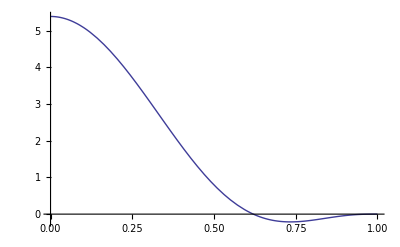

```mathematica
(* 
Given a blob, compute all formulas for Sooklets with compact support. 
We compute functions related to the Stokeslet and the rotlets for the same blob 
*)

(* Clear all variables first *)
Clear["Global`*"]
$Assumptions={r>0,d>0,R>d,z>0};

(* Define a blob. Choose one *)
(* blob = 105/(32*Pi)*(1-r^2/d^2)^2/d^3 *)
 (* blob = 315/(128*Pi)*(5-11*r^2/d^2)*(1-r^2/d^2)^2/d^3 *)
blob = 17325/(1024*Pi)*(1-13/5*r^2/d^2)*(1-r^2/d^2)^3/d^3 

(* check integral = 1 and check second moment 
THM: the functions H1 and H2 for d<r will match the singular formulas 
if and only if the blob integral is 1 and second moment is 0. *)
Integrate[4*Pi*r^2*blob,{r,0,d}]
Integrate[4*Pi*r^4*blob,{r,0,d}]
Plot[blob/.d->1,{r,0,1}]
```

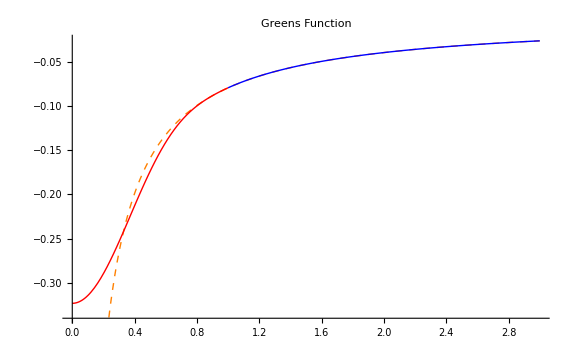

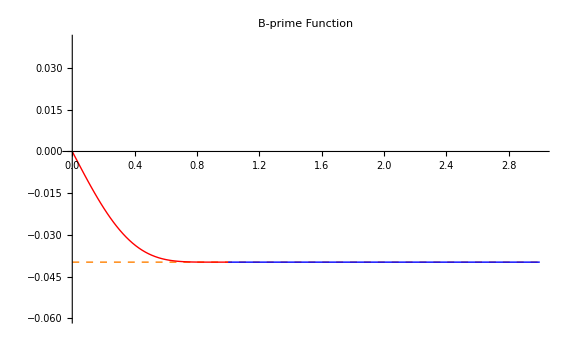

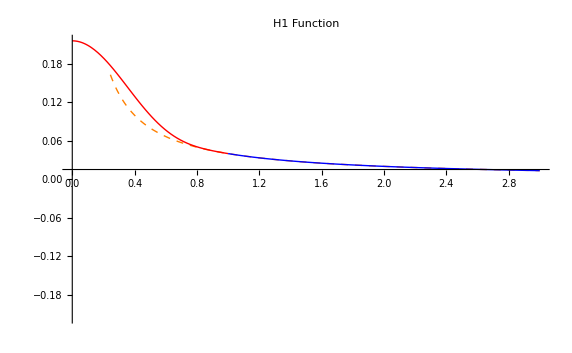

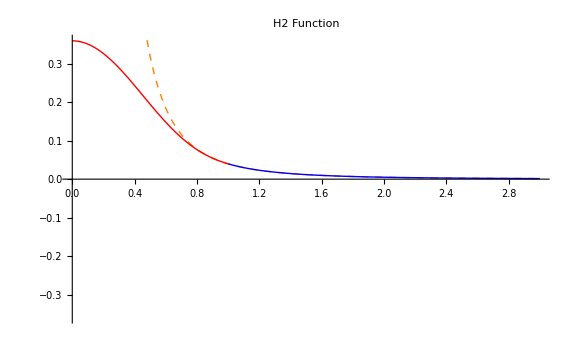

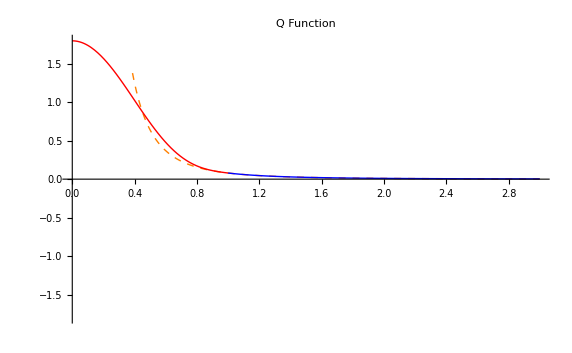

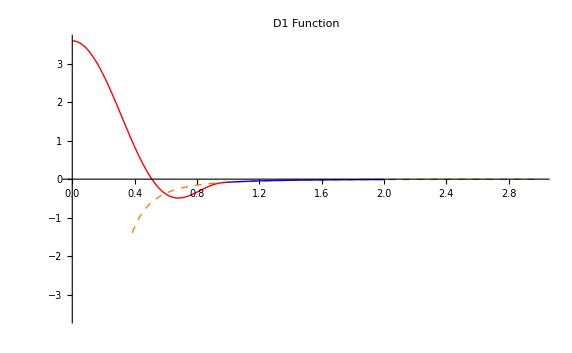

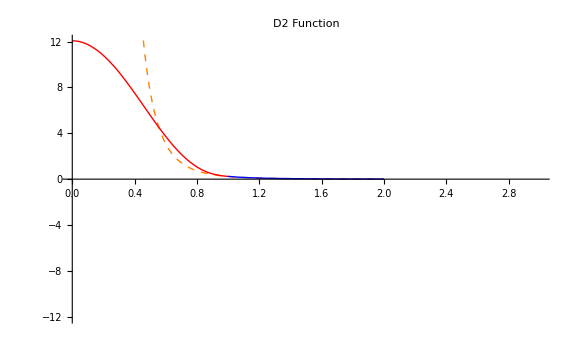

```mathematica
(* Find the functions for Stokeslet Velocity *)
(* Suppose g(r)= g_in(r) when r<d and g(r)=g_out(r) when d<r 
To solve f"(r) + 2*f'(r)/r = g(r) we do the following:
	Let A = r^2*f'(r) and so we solve A'(r) = g(r) using A(0)=0
	For r<d:  
		A_in(r) = Integrate[s*g_in(s),{s,0,r}]
	For d<r:
		A_out(r) = Integrate[s*g_in(s),{s,0,d}] + Integrate[s*g_out(s),{s,d,r}] 
	Once we have A(r) we have to solve r^2*f'(r) = A(r). Here we don't know f(0)
	so we do the following:
	For r<d:
		f(r) = Integrate[A_in(r)/r^2,r]+c1
	For d>r:
		f(r) = Integrate[A_in(r)/r^2,{r,0,d}]+Integrate[A_out(r)/r^2,r]+c1
	and set c1 by matching f(r) to the exact solution for r>>1 if possible *)
 
Ain=(Integrate[r^2*blob,{r,0,R}]/.R->r);
Aout=Integrate[r^2*blob,{r,0,d}]+(Integrate[r^2*0,{r,d,R}]/.R->r);
GI=Expand[(Integrate[Ain/r^2,{r,0,R}]/.R->r)+c1];
GO=Expand[Integrate[Ain/r^2,{r,0,d}]+Integrate[Aout/r^2,{r,d,R}]/.R->r]+c1;
sol=Solve[GO+1/(4*Pi*r)==0,c1];
GI = GI/.sol[[1]];
GO = GO/.sol[[1]];
	p1=Plot[GI/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[GO,{r,1,3},PlotStyle->Blue];
	p3 = Plot[-1/(4*Pi*r),{r,0,3},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotLabel->"Greens Function"]
(* Find B'(r) for r<d and for r>d *)
BpI=(Integrate[r^2*GI,{r,0,R}]/.R->r)/r^2;
BpO=(Integrate[r^2*GI,{r,0,d}]+(Integrate[r^2*GO,{r,d,R}]/.R->r))/r^2;
	p1=Plot[BpI/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[BpO/.d->1,{r,1,3},PlotStyle->Blue];
	p3 = Plot[-1/(8*Pi),{r,0,3},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotRange->{{0,3},{-1.5/(8*Pi),1/(8*Pi)}},PlotLabel->"B-prime Function"]

H1I = Simplify[Simplify[BpI/r-GI]];
H1O = Expand[Simplify[BpO/r-GO]];
	p1=Plot[H1I/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[H1O/.d->1,{r,1,3},PlotStyle->Blue];
	p3 = Plot[1/(8*Pi*r),{r,0,3},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotRange->{{0,3},{-(H1I/.{d->1,r->0}),(H1I/.{d->1,r->0})}},PlotLabel->"H1 Function"]

H2I = Simplify[(r*D[BpI,r]-BpI)/r^3];
H2O = Simplify[(r*D[BpO,r]-BpO)/r^3];
	p1=Plot[H2I/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[H2O/.d->1,{r,1,3},PlotStyle->Blue];
	p3 = Plot[1/(8*Pi*r^3),{r,0,3},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotRange->{{0,3},{-(H2I/.{d->1,r->0}),(H2I/.{d->1,r->0})}},PlotLabel->"H2 Function"]

(* Find all other functions *)
QI = Simplify[D[GI,r]/r];
QO = Simplify[D[GO,r]/r];
	p1=Plot[QI/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[QO/.d->1,{r,1,3},PlotStyle->Blue];
	p3 = Plot[1/(4*Pi*r^3),{r,0,3},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotRange->{{0,3},{-(QI/.{d->1,r->0}),(QI/.{d->1,r->0})}},PlotLabel->"Q Function"]

D1I = Simplify[blob-D[GI,r]/r];
D1O = Simplify[0 - D[GO,r]/r];
	p1=Plot[D1I/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[D1O,{r,1,2},PlotStyle->Blue];
	p3 = Plot[-1/(4*Pi*r^3),{r,0,3},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotRange->{{0,3},{-(D1I/.{d->1,r->0}),(D1I/.{d->1,r->0})}},PlotLabel->"D1 Function"]

D2I=Simplify[-(r*D[D[GI,r],r]-D[GI,r])/r^3];
D2O=Simplify[-(r*D[D[GO,r],r]-D[GO,r])/r^3];
	p1=Plot[D2I/.d->1,{r,0,1},PlotStyle->Red];
	p2 =Plot[D2O,{r,1,2},PlotStyle->Blue];
	p3 = Plot[3/(4*Pi*r^5),{r,0,2},PlotStyle->{Orange,Dashed}];
	Show[p3,p1,p2,PlotRange->{{0,3},{-(D2I/.{d->1,r->0}),(D2I/.{d->1,r->0})}},PlotLabel->"D2 Function"]
```

```mathematica
(* Summary of Functions *)
GI = (Factor[(GI/.r->d*Sqrt[z])-(GO/.r->d)]+(GO/.r->d))/.z->(r^2/d^2);
GO=Expand[GO];
"Q(r)=G'(r)/r function for 0<r<d and for d<r:"
QI = (Factor[(QI/.r->d*Sqrt[z])-(QO/.r->d)]+(QO/.r->d))/.z->(r^2/d^2)
QO=Expand[QO]
"H1(r) function for 0<r<d and for d<r:"
H1I = (Factor[(H1I/.r->d*Sqrt[z])-(H1O/.r->d)]+(H1O/.r->d))/.z->(r^2/d^2)
H1O=Expand[H1O]
"H2(r) function for 0<r<d and for d<r:"
H2I = (Factor[(H2I/.r->d*Sqrt[z])-(H2O/.r->d)]+(H2O/.r->d))/.z->(r^2/d^2)
H2O=Expand[H2O]
"D1(r) function for 0<r<d and for d<r:"
D1I = (Factor[(D1I/.r->d*Sqrt[z])-(D1O/.r->d)]+(D1O/.r->d))/.z->(r^2/d^2)
D1O=Expand[D1O]
"D2(r) function for 0<r<d and for d<r:"
D2I = (Factor[(D2I/.r->d*Sqrt[z])-(D2O/.r->d)]+(D2O/.r->d))/.z->(r^2/d^2)
D2O=Expand[D2O]
```

Q(r)=G'(r)/r function for 0<r<d and for d<r:

1/(4 d^3 π)+((-1+r^2/d^2) (-5519+(13885 r^2)/d^2-(12845 r^4)/d^4+(4095 r^6)/d^6))/(1024 d^3 π)

1/(4 π r^3)

H1(r) function for 0<r<d and for d<r:

1/(8 d π)-((-1+r^2/d^2) (565-(1745 r^2)/d^2+(2413 r^4)/d^4-(1547 r^6)/d^6+(378 r^8)/d^8))/(1024 d π)

1/(8 π r)

H2(r) function for 0<r<d and for d<r:

1/(8 d^3 π)+((-1+r^2/d^2) (-1027+(1745 r^2)/d^2-(1225 r^4)/d^4+(315 r^6)/d^6))/(1024 d^3 π)

1/(8 π r^3)

D1(r) function for 0<r<d and for d<r:

-1/(4 d^3 π)+((-1+r^2/d^2) (-5903+(32905 r^2)/d^2-(47285 r^4)/d^4+(20475 r^6)/d^6))/(512 d^3 π)

-1/(4 π r^3)

D2(r) function for 0<r<d and for d<r:

3/(4 d^5 π)-(15 (-1+r^2/d^2) (317-(574 r^2)/d^2+(273 r^4)/d^4))/(128 d^5 π)

3/(4 π r^5)